# Throwing Dice

In this notebook, we'll simulate the rolling of dice.

## Clear symbols

In order to avoid interference from symbols defined in other notebooks, we first Clear and Remove all symbols.  We assume that the relevant symbols are in the Global` context.

```mathematica
Clear["Global`*"]
```

```mathematica
Remove["Global`*"]
```

## Load some useful packages

If you are using a Mathematica version 6 or earlier, you will need to "uncomment" the following line (which means removing "(*" and "*)".  These functions are now built-in from version 7 on.

```mathematica
(*  <<"BarCharts`";<<"Histograms`"; *)
```

## Simulate the dice!

Possible outcomes of throwing a single die:

```mathematica
dots = {1,2,3,4,5,6}
```

{1,2,3,4,5,6}

We define a uniform probability distribution for the results 1 to 6, and call it "dice":

```mathematica
dice ={1,6};
```

How many times we toss the die => trials:

```mathematica
trials = 120;
```

Toss it (suppressing output with a ; when trials is large):

```mathematica
toss = RandomInteger[dice,trials];
```

```mathematica
?RandomInteger
```

Count how many of each number (between 1/2 and 3/2, 3/2 and 5/2, etc):

```mathematica
freq = BinCounts[toss,{.5,6.5,1}]
```

{15,25,25,21,12,22}

```mathematica
?BinCounts
```

Plot the frequency of each result as a histogram:

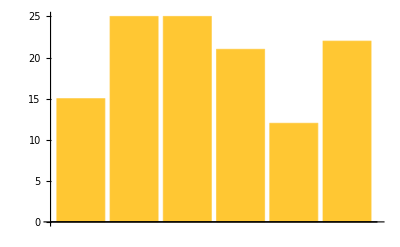

```mathematica
BarChart[freq]
```

Efficient way to add up the elements of the list "dots" ==>  Apply the "Plus" operator to each element:

```mathematica
Plus @@ dots
```

21

Calculate the average value of the number of dots:

```mathematica
N[ Plus @@ (freq*dots) / trials ]
```

3.46667

Calculate the average value of the number of dots squared:

```mathematica
N[ Plus @@ (freq*dots^2) / trials ]
```

14.7333

Let's define a function that combines all of these steps:

```mathematica
Rolldice[trials_] := (
dots = {1,2,3,4,5,6};
dice ={1,6};
toss = RandomInteger[dice,trials];
freq=BinCounts[toss,{.5,6.5,1}];
avgdots = N[Plus@@(freq*dots)/trials];
avgdotssq = N[Plus@@(freq*dots^2)/trials];
sdev = Sqrt[avgdotssq-avgdots^2];
Print["mean = ",avgdots,"  standard deviation = ",sdev];
BarChart[freq] )
```

mean = 3.25  standard deviation = 1.87639

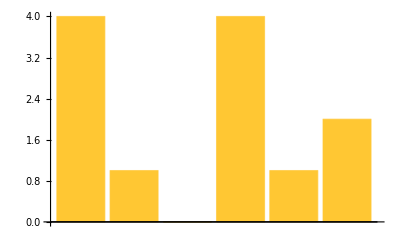

```mathematica
Rolldice[12]
```

mean = 3.49167  standard deviation = 1.71268

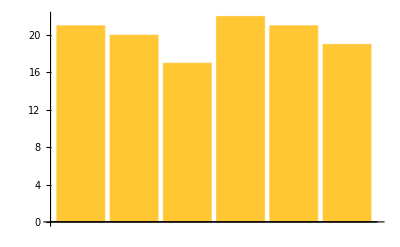

```mathematica
Rolldice[120]
```

mean = 3.5375  standard deviation = 1.73981

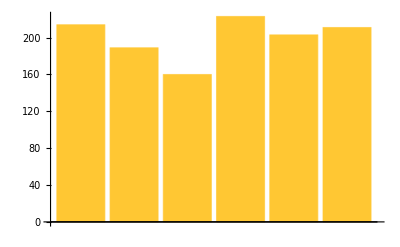

```mathematica
Rolldice[1200]
```

mean = 3.50075  standard deviation = 1.71503

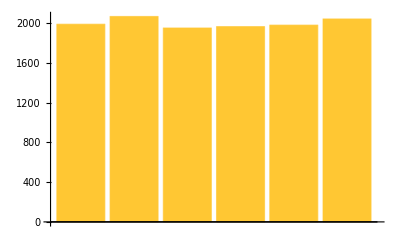

```mathematica
Rolldice[12000]
```

mean = 3.4942  standard deviation = 1.70162

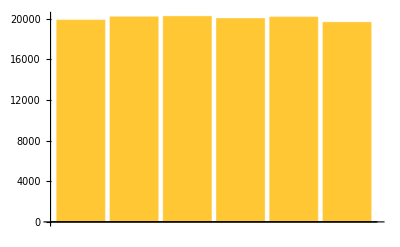

```mathematica
Rolldice[120000]
```

mean = 3.49957  standard deviation = 1.70813

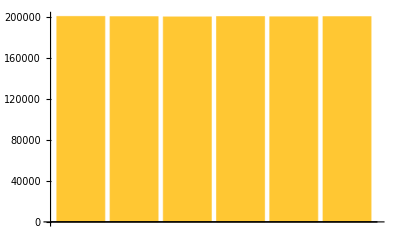

```mathematica
Rolldice[1200000]
```